```mathematica
(* Ganz unten sieht ,man, dass noch ein Fehler in der Routine GeradenPixelDetektion steckt *)

TestBildDaten={{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1,0,0}};
TestBild=Image[TestBildDaten];
TestBild=ColorConvert[TestBild, "RGB"];Show[TestBild,  Plot[x*3/10,{x,0,10}, PlotStyle->Red], Axes->True, ImageSize->Large]
```

```mathematica
SchnittmitHorizontalen[Bild_, GeradenAusdruck_]:=
Module[{BildHoehe, BildBreite, m,b, x,SchnittPunktListeHorizontal={}},
BildHoehe=Dimensions[ImageData[Bild ]][[1]];
BildBreite=Dimensions[ImageData[Bild ]][[2]];
m=Coefficient[GeradenAusdruck[x],x,1];
b=Coefficient[GeradenAusdruck[x],x,0];

For[y=0,y≤ BildHoehe, y++,
If[m!=0, x=(y-b)/m, Break[]];
If[x≥ 0 && x≤ BildBreite, 
AppendTo[SchnittPunktListeHorizontal, {x,y}], Continue[]
] (*End If*)
] (* End For*);
SchnittPunktListeHorizontal
]; (* End Module *)

SchnittmitVertikalen[Bild_, GeradenAusdruck_]:=
Module[{BildHoehe, BildBreite, m,b, x,SchnittPunktListeVertikal={}},
BildHoehe=Dimensions[ImageData[Bild ]][[1]];
BildBreite=Dimensions[ImageData[Bild ]][[2]];
m=Coefficient[GeradenAusdruck[x],x,1];
b=Coefficient[GeradenAusdruck[x],x,0];

For[x=0,x≤ BildBreite, x++,
If[m!=0, y=m*x+b, Break[]];
If[y≥ 0 && y≤ BildHoehe, 
AppendTo[SchnittPunktListeVertikal, {x,y}], Continue[]
] (*End If*)
] (* End For*);
SchnittPunktListeVertikal
]; (* End Module *)


GeradenPixelDetektion[Bild_,GeradenAusdruck_]:=Module[{BildHoehe, BildBreite, SpListeVertikal, SpListeHorizontal, GetroffenePixelListe={},x,y, BildMatrixNeu},
BildHoehe=Dimensions[ImageData[Bild ]][[1]];
BildBreite=Dimensions[ImageData[Bild ]][[2]];

SpListeVertikal=SchnittmitVertikalen[Bild,GeradenAusdruck];
For[SPZaehler=1,SPZaehler≤ Length[SpListeVertikal], SPZaehler++,
x=SpListeVertikal[[SPZaehler,1]] ;
y=BildHoehe-Floor[   SpListeVertikal[[SPZaehler,2]] ];
If[y≠0,
If[x==0,AppendTo[GetroffenePixelListe, {y,1}],
AppendTo[ GetroffenePixelListe, {y,x}];
If[x≠ BildBreite,AppendTo[GetroffenePixelListe,  {y,x+1}]
];
];
, Continue[]];
];

SpListeHorizontal=SchnittmitHorizontalen[Bild,GeradenAusdruck];
For[SPZaehler=1,SPZaehler≤ Length[SpListeHorizontal], SPZaehler++,
x=Floor[SpListeHorizontal[[SPZaehler,1]] ]+1 ;
y=   SpListeHorizontal[[SPZaehler,2]] ;
If[x≠BildBreite+1,
If[y==0,
AppendTo[GetroffenePixelListe, {BildHoehe,x}],
AppendTo[GetroffenePixelListe, {BildHoehe-y+1,x}],
If[y≠ BildHoehe,
AppendTo[GetroffenePixelListe, {BildHoehe-y,x}],
];
];
,Continue[]];
];

GetroffenePixelListe= DeleteDuplicates[GetroffenePixelListe];

GetroffenePixelListe
];

SchnittPixelDetektion[Bild_,GeradenAusdruck_]:=Module[{BildHoehe, BildBreite, SpListeVertikal, SpListeHorizontal, GeradenPixelListe={}, KantenPixelListe={}, BildMatrixNeu},
GeradenPixelListe=GeradenPixelDetektion[Bild,GeradenAusdruck];

BildHoehe=Dimensions[ImageData[Bild ]][[1]];
BildBreite=Dimensions[ImageData[Bild ]][[2]];
For[i=1,i≤ BildBreite,i++,
For[j=1,j≤ BildHoehe,j++,
If[ImageData[Bild][[j,i]]=={1,1,1}, AppendTo[KantenPixelListe,{j,i}]
] (* End If*)
];
];
Print["TestAusgabe Kanten"];
Print[KantenPixelListe];
Print["Ende TestAusgabe Kanten"];

BildMatrixNeu=ImageData[Bild];
For[PixelZaehler=1, PixelZaehler≤ Length[GeradenPixelListe], PixelZaehler++,
Print[ GeradenPixelListe[[ PixelZaehler   ]] ];
If[MemberQ[KantenPixelListe,  GeradenPixelListe[[ PixelZaehler   ]]],
BildMatrixNeu[[  GeradenPixelListe[[ PixelZaehler  ]][[1]],GeradenPixelListe[[ PixelZaehler ]][[2]]
]] ={1,0,0},
BildMatrixNeu[[  GeradenPixelListe[[ PixelZaehler  ]][[1]],GeradenPixelListe[[ PixelZaehler ]][[2]]
]] ={0,0.5,0.5};
];
];


BildMatrixNeu

];




KontrollAusgabe[Bild_, GeradenAusdruck_]:=
Module[{BildMatrixNeu},
BildMatrixNeu=SchnittPixelDetektion[Bild,GeradenAusdruck];
Show[Image[BildMatrixNeu], Plot[GeradenAusdruck[x],{x,0,10}, PlotStyle->Red],
  Axes->True, AspectRatio->Automatic,ImageSize->Large ]
];
```

TestAusgabe Kanten

{{1,6},{2,7},{3,8}}

Ende TestAusgabe Kanten

{3,1}

{3,2}

{3,3}

{3,4}

{2,4}

{2,5}

{2,6}

{2,7}

{1,7}

{1,8}

{1,9}

{1,10}

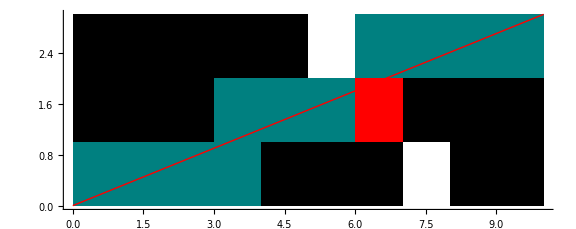

```mathematica
KontrollAusgabe[TestBild,Function[x,x*3/10]]
```

TestAusgabe Kanten

{{1,6},{2,7},{3,8}}

Ende TestAusgabe Kanten

{3,1}

{3,2}

{3,3}

{2,3}

{2,4}

{2,5}

{2,6}

{1,6}

{1,7}

{1,8}

{1,9}

{3,4}

{2,7}

{1,10}

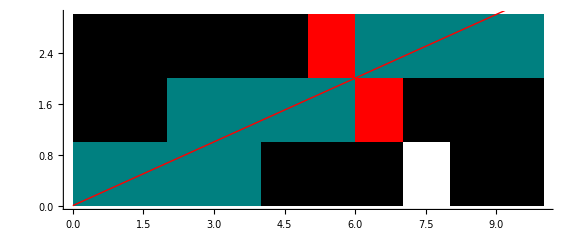

```mathematica
KontrollAusgabe[TestBild,Function[x,x/3]]
```

TestAusgabe Kanten

{{1,6},{2,7},{3,8}}

Ende TestAusgabe Kanten

{3,1}

{3,2}

{2,2}

{2,3}

{2,4}

{1,4}

{1,5}

{1,6}

{3,3}

{2,5}

{1,7}

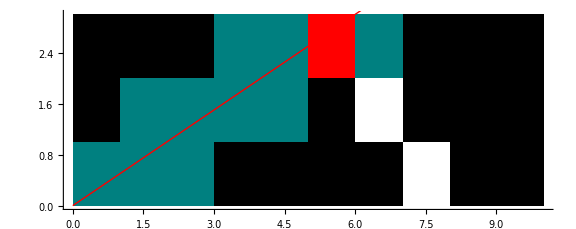

```mathematica
KontrollAusgabe[TestBild,Function[x,x/2]]
```

TestAusgabe Kanten

{{1,6},{2,7},{3,8}}

Ende TestAusgabe Kanten

{3,1}

{1,1}

{1,2}

{2,2}

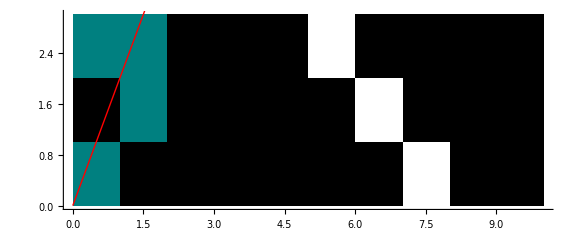

```mathematica
KontrollAusgabe[TestBild,Function[x,2x]]
```